```mathematica
Remove["Global`*"]
```

The algorithm

To start the simulation, we set U as an alias of the uniformly-distributed random number generator from 0 to 1, and NormalDist as an alias of the normally-distributed random number generator from 0 to 1. The algorithm for NormalDist is based on a 2-variable generator in polar coordinate as it is easier to generate them, then we only take one and discard the other. The printing variable denotes whether the modules should print out every result - when we just simulate one election, it should be turned on so that the detail are transparent, but when we simulation 10,000 of them to see the general behavior, printing everything out will exhaust the machine’s resource and most likely cause everything to hang.

```mathematica
U:=Random[];
NormalDist:=√(-2Log[U])Cos[2π*U]; (*Normal Random Variable*)
```

Swing state simulation process

The module swingState takes in 5 parameters, respectively: the name of the state, number of electoral votes of that state, the percentage of population in the state voting for Red, the percentage of population in the state voting for Blue, and the Margin of Error.
First, we calculate the percentage of population in the State who actually voted for Red by correcting the Red voters data from the poll using the Margin of Error. The way we treated the Margin of Error is by creating a Normal Random Variable whose standard deviation is half of the Margin of Error. By this way, 95% of the variables will fall between the range given by the Margin of Error, although it will most likely be 0, denoting that the polling data is correct; and its minimum and maximum values are the negation of the Margin of Error, and the Margin of Error itself, respectively.
Second, we repeat the aforementioned procedure to calculate the percentage of population in the state who actually voted for Blue. Then, we can calculate the percentage of population who are still undecided, or casted a blank vote by subtracting the percentage of voters for Red and Blue from 100.
For some states, the Margin of Error is too large, making the simulation unreliable and the percentage of undecided population negative. In that case, we ignore the result and regenerate the outcome. Else, we proceed to add all the electoral votes of that state to the winning side, then print out the details if printing is set to 1. Finally, the module returns -1 if Red wins, and 1 if Blue wins, then terminates.

```mathematica
(* define a function that determines the winner in a state *)
swingState[State_,EV_,R_,B_,MoE_]:=Module[{Un,Win,redPer,bluePer,val},

redPer=R+MoE*NormalDist/2; (* percentage of votes on Red ± a uniform random value within the Margin of Error *)
bluePer=B+MoE*NormalDist/2; (* percentage of votes on Blue ± a uniform random value within the Margin of Error *)
Un=100-redPer-bluePer; (* Rest of the votes is undecided*)

If[Un<0,swingState[State,EV,R,B,MoE],
If[redPer>bluePer,
Win="Red"; redEV=redEV+EV, (* Red wins in the state *)
Win="Blue";blueEV=blueEV+EV]; (* Blue wins in the state *) 

printResult[State,EV,redPer,bluePer,Un,Win]; (* Append the result to the table *)
val=If[redPer>bluePer,-1,1];
Return[val];
]
];
```

Election simulation process

The module election simulates the election, and requires no parameter. It starts with initiating a 2-dimentional string array of swing states’ voting data with the legends - in layman’s term, it’s a table of data with the first row being the explanation of each column; and each simulated swing state’s data will get appended to the table. Then we set the electoral votes of non-swing states to both sides of the election as the initial value, which would then get incremented in the swingState module. After that, we run the simulation of all the 9 swing states’ voting to get the final result of the election. If printing is set to 1, the aforementioned completed table will get printed out. Finally, it returns an array of two value: result, which is 0 if Red wins, 1 if Blue wins, and 2 if it’s a draw, and landslide, which is 0 if Red wins in a landslide (i.e. Red wins with more than 300 electoral votes), 1 if Blue wins in a landslide, and Null otherwise.

```mathematica
election:=Module[{result=0,landslide=0},
(* turn on or off print statements throughout the code *)
printing=0;

printTable={{"State","EV","Red %", "Blue %","Undecided","Win"}};
printResult[State_, EV_, R_,B_,Un_,Win_]:=AppendTo[printTable,{State,EV,R,B,Un,Win}];

(* given Electoral Votes to Red and Blue from other states *)
redEV=206;
blueEV=212;

(* determine the winners in each state *)
swingState["Florida",29,47,44,1];
swingState["Pennsylvania",20,46,47,2.5];
swingState["Ohio",18,48,46,2];
swingState["Virginia",13,47,46,1.5];
swingState["Indiana",11,48,48,3];
swingState["Missouri",10,49,48,0.5];
swingState["Colorado",9,45,48,1.5];
swingState["Kansas",6,45,46,0.5];
swingState["Iowa",6,44,48,3.5];


(* turn on or off the printing function *)
If[printing==1,Print[Grid[printTable,Frame->All,Alignment->{{Center,"."}},Background->{None,{{LightBlue,None}}}]];];

(*if Red has more electoral votes, Red wins; if Blue has more, Blue wins; else they tie *)
result=Which[redEV>blueEV,0,blueEV>redEV,1,redEV=blueEV,2];
landslide=Which[redEV>300,0,blueEV>300,1]; 
Return[{result,landslide}]
]
```

Swing state analysis

The States module runs each swing state election simulation 1,000 times, then calculate the percentage that each side wins and prints out the calculated data in a table form.

```mathematica
(* Module that returns the probility of winning for both sides in each state in a table after 1,000 times of simulation  *)
```

```mathematica
States:=Module[{},
StateTable={{"State","EV","Red Win %", "Blue Win %"}};

Florida=Count[Table[swingState["Florida",29,47,44,1],1000],-1]/10.;
Penn=Count[Table[swingState["Pennsylvania",20,46,47,2.5],1000],-1]/10.;
Ohio=Count[Table[swingState["Ohio",18,48,46,2],1000],-1]/10.;
Virginia=Count[Table[swingState["Virginia",13,47,46,1.5],1000],-1]/10.;
Indiana=Count[Table[swingState["Indiana",11,48,48,3],1000],-1]/10.;
Missouri=Count[Table[swingState["Missouri",10,49,48,0.5],1000],-1]/10.;
Colorado=Count[Table[swingState["Colorado",9,45,48,1.5],1000],-1]/10.;
Kansas=Count[Table[swingState["Kansas",6,45,46,0.5],1000],-1]/10.;
Iowa=Count[Table[swingState["Iowa",6,44,48,3.5],1000],-1]/10.;

AppendTo[StateTable,{"Florida",29,Florida,100-Florida}];
AppendTo[StateTable,{"Pennsylvania",20,Penn,100-Penn}];
AppendTo[StateTable,{"Ohio",18,Ohio,100-Ohio}];
AppendTo[StateTable,{"Virginia",13,Virginia,100-Virginia}];
AppendTo[StateTable,{"Indiana",11,Indiana,100-Indiana}];
AppendTo[StateTable,{"Missouri",10,Missouri,100-Missouri}];
AppendTo[StateTable,{"Colorado",9,Colorado,100-Colorado}];
AppendTo[StateTable,{"Kansas",6,Kansas,100-Kansas}];
AppendTo[StateTable,{"Iowa",6,Iowa,100-Iowa}];

Print[Grid[StateTable,Frame->All,Alignment->{{Center,"."}},Background->{None,{{LightBlue,None}}}]];
]
```

The actual simulation

We then test the election simulation module by running it once. Returning  {0, Null}, it says that Red wins without a landslide. Then, we proceed to find out the general behavior of the simulation by running election module 10,000 times, and make a table called Data. The first column of the data that contains the results of the election is then stored in a table ElectionResult and the landslide results in LandslideData.

```mathematica
election
```

State | EV | Red % | Blue % | Undecided | Win
Florida | 29 | 46.7211 | 42.6428 | 10.6362 | Red
Pennsylvania | 20 | 44.9225 | 48.7735 | 6.30403 | Blue
Ohio | 18 | 48.0379 | 45.6788 | 6.28333 | Red
Virginia | 13 | 45.4562 | 45.3785 | 9.1653 | Red
Indiana | 11 | 50.8267 | 48.7926 | 0.380661 | Red
Missouri | 10 | 48.8195 | 47.9795 | 3.201 | Red
Colorado | 9 | 46.5017 | 48.4264 | 5.07193 | Blue
Kansas | 6 | 44.8531 | 45.9941 | 9.15278 | Blue
Iowa | 6 | 43.4136 | 48.8337 | 7.75272 | Blue

{0,Null}

```mathematica
Data=Table[election,{10000}];
ElectionResult=Table[Data[[n,1]],{n,1,10000}];
```

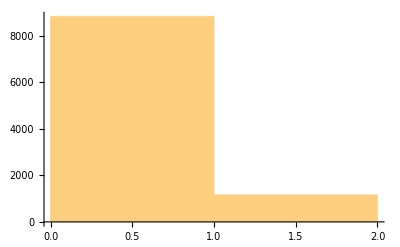

```mathematica
Histogram[ElectionResult,{1}]
```

```mathematica
PieChart3D[{Count[Data,0],Count[Data,1],Count[Data,2]}]
```

-Graphics3D-

```mathematica
LandslideData=Table[Data[[n,2]],{n,1,10000}];
```

```mathematica
Count[LandslideData,1]/10000.
Count[LandslideData,0]/10000.
```

0.

0.1201

```mathematica
States
```

State | EV | Red Win % | Blue Win %
Florida | 29 | 100. | 0.
Pennsylvania | 20 | 27.2 | 72.8
Ohio | 18 | 92.5 | 7.5
Virginia | 13 | 81.5 | 18.5
Indiana | 11 | 52.3 | 47.7
Missouri | 10 | 99.8 | 0.2
Colorado | 9 | 0.1 | 99.9
Kansas | 6 | 0.4 | 99.6
Iowa | 6 | 5.1 | 94.9